Worksheet 3, Math 152      *      D. Maslanka         *     Fall 2015

DIRECTION FIELDS AND EULER'S METHOD

Goals:  In this worksheet differential equations and initial value problems are solved with  Mathematica.
The notion of a slope field and Euler's Method for approximating solutions to DE's are 
described and then visualized in an example that utilizes some  Mathematica  system-based instructions.

I. Slope Fields
Recall that if we are given a differential equation

                                               dy/dx  =  F ( x , y )
 and any point  P_1 = (x_o , y_o) ,  in the domain of   F, then we know that   F (x_1 , y_1)  represents the
  slope of a solution curve when passing through the point P_1  . 
  If we draw a short directed line segment having slope   F  (x , y )  at a large number of points  
  P  = ( x , y ) ,  then the result is called a slope field or direction field. A slope field is used to visualize 
  the general shapes of solution curves.  Slope fields can be generated using  Mathematica. 
  
  We obtain this field using the command VectorPlot. VectorPlot is meant to visualize velocity fields.
  It takes three agruments:
	• The first argument is a list showing the velocities (or rates of change) in the x and y directions, 
	   respectively. For a differential equation of the form  dy/dx=f(x,y),  this will always be 
	  {1,f[x,y]}  since dx/dx=1.
  	• The second and third arguments are the range over which to plot. Just like with the Plot command, 
  	   these are of the form {variable, lowerbound, upperbound}.
  	   
  Consider the differential equation:
  
                                  dy/dx  = ⅇ^(-x)-2y                  ( 1 ) 
                                               
We first define the derivative, dy/dx , in  (1)  as a function of two variables and then plot its slope field.

```mathematica
Clear[x,y]
f[x_, y_]:= Exp[-x]-2*y 
"f(x,y)="f[x,y]
VectorPlot[{1,f[x,y]},{x,-4,4},{y,-4,4},Axes->True]
```

By default, the lengths of the arrows are dependent of the relative magnitudes of the slopes. This can make the plot 
very difficult to read since some arrows are very small.
In order to change the relative sizes of the arrows, we use the VectorScale option. VectorScale is passed as a
list: the first item in the list is the thickness of the arrow as a whole, the second is the thickness of the head only, and the 
third is how they scale with magnitude. Useful options are Tiny, Small, Medium, Large, and Automatic 
for the first two, (decimal values may also be used in these positions) and None and Automatic for the last.

```mathematica
Slopefield=VectorPlot[{1,f[x,y]},{x,-4,4},{y,-4,4},VectorScale-> {Tiny,Small,None},VectorStyle->Lighter[Gray],Axes->True]
```

We may even ask  Mathematica  to plot the solution curves passing through twenty randomly selected initial points by 
adding the option: StreamPoints→20 to the VectorPlot instruction:

```mathematica
VectorPlot[{1,f[x,y]},{x,-4,4},{y,-4,4},VectorStyle->Lighter[Gray],VectorScale-> {Tiny,Tiny,None},Axes->True,StreamPoints-> 20]
```

Allternatively, we may specify the particular set of initial points that the solution curves should pass through.

```mathematica
VectorPlot[{1,f[x,y]},{x,-4,4},{y,-4,4},VectorScale-> {Tiny,Tiny,None},Axes->True,AxesStyle->Black,VectorStyle->Lighter[Gray],StreamPoints-> {{-3,2},{-2,2},{0,1},{-1/2,0},{0,2},{0,-2},{2,1/2},{2,-1/2}}]
```

The additional option, StreamStyle,can be used to further control the look of the solution curves:

```mathematica
VectorPlot[{1,f[x,y]},{x,-4,4},{y,-4,4},VectorScale-> {Tiny,Tiny,None},Axes->True,AxesStyle->Black,VectorStyle->Lighter[Gray],StreamPoints-> {{-3,2},{-2,2},{0,1},{-1/2,0},{0,2},{0,-2},{2,1/2},{2,-1/2}},StreamStyle->{Darker[Blue],Thickness[0.005]}]
```

II. Euler's Method
Euler's Method uses the idea of slope fields to obtain approximate solutions to the initial value problem :        
              	      dy/dx  =  F ( x , y ) ,     y ( x_1 )  =  y_1    as follows.
              	      
 Let    P_1 = (x_1 , y_1),  P_2 = (x_2 , y_2) ,  P_3 = (x_3 , y_3) , . . . ,  P_(n+1) = (x_(n+1) , y_(n+1))   where    
     
 		x_2 =  x_1 + h 		    y_2 =  y_1 + F (x_1 , y_1) · h      
		x_3 =  x_2 + h 		    y_3 =  y_2 + F (x_2 ,y_2) · h      
		x_4 =  x_3 + h 		    y_4 =  y_3 + F (x_3 , y_3) · h      
	     	      • 			  	• 
	     	      • 		  		• 
	  	      • 				•
	 	      • 				• 
		 x_(n+1) =  x_n + h	                      y_(n+1) =  y_n + F (x_n , y_n) · h

We test this method on the initial value problem :

                                  dy/dx  = ⅇ^(-x)-2y    ,  y  (-2) = -2              ( 2 ) 
                                               
 over the x-interval  I  =  [ -2 , 4 ]. We begin by using a large step size, say  h = 0.5 , (this number represents the 
 difference between the  x-coordinates of   P_( i+1)    and    P_i    for  i  =  0 , 1 , 2 ,  .  .  . , n ).

```mathematica
h=0.5;
```

Let's refer to the left and right endpoints of the interval  I  as  a  and  b  respectively.

```mathematica
a=-2;(* I = [a,b] is the x-interval for the Euler solution *)
b=4;
```

Observe that there are n = (b-a)/h  nonoverlapping intervals of length  h  that cover the interval  I.  We input this
information, as well as the  x  and  y  coordinates of the initial point, P_1 .

```mathematica
n=Floor[(b-a)/h];
n"=number of subintervals of length h in [a,b]"
f[x_,y_]:=N[Exp[-x]]-2*y;

x=ConstantArray[0,n+1]
y=ConstantArray[0,n+1]

x[[1]]=-2  (* x[[1]] and y[[1]] are the x and y coordinates of P1 *)
y[[1]]=-2
```

Now let's iterate over the  n = 12 steps. We will use the variable  i  to indicate the current step

```mathematica
Do[
x[[i+1]]=x[[i]]+h;
y[[i+1]]=y[[i]]+f[x[[i]],y[[i]]]*h;,
{i,1,n}]
x
y
```

We now have two filled arrays of numbers: the first array lists all of the x values, and the second one, lists all of the 
corresponding  y values for the vertices of the Euler approximation. In order to plot them, we will need a to form a 
related list of x,y pairs. We accomplish this with the Table command:

```mathematica
Eulerpts1=Table[{x[[i]],y[[i]]},{i,1,n+1}]
```

Now to plot them, we use the  ListPlot command:

```mathematica
ListPlot[Eulerpts1]
```

The points we have plotted can be connected using the Joined option:

```mathematica
Euler12=ListPlot[Eulerpts1, Joined-> True,PlotMarkers->{Automatic,Tiny},PlotStyle->{Darker[Green],Thickness[0.003]}]
```

In the above application of Euler's Method, observe that the slope of the Euler solution curve was changed every
1/2 unit, (as  h =1/2), based on the steepness of the slope field.  We may improve the accuracy of the approximation 
by reducing the value of the step size, h. In case we apply Euler's Method when h = 1/10 , we obtain:

```mathematica
h=1/10
a=-2;(* I = [a,b] is the x-interval for the Euler solution *)
b=4;
n=Floor[(b-a)/h];
n"=number of subintervals of length h in [a,b]"
f[x_,y_]:=Exp[-x]-2*y;

x=ConstantArray[0,n+1];
y=ConstantArray[0,n+1];

x[[1]]=-2  (* x[[1]] and  y[[1]] are the x and y coordinates of P1 *)
y[[1]]=-2

Do[
x[[i+1]]=x[[i]]+h;
y[[i+1]]=y[[i]]+N[f[x[[i]],y[[i]]]]*h;,
{i,1,n}]

Eulerpts2=Table[{x[[i]],y[[i]]},{i,1,n+1}];
Euler60=ListPlot[Eulerpts2, Joined-> True,PlotMarkers->{Automatic,Tiny},PlotStyle->{Blue,Thickness[0.003]}]
```

Now, we display both Euler approximations as well as the underlying slope field on the same plot.

```mathematica
Show[{Euler12,Euler60,Slopefield},AspectRatio->Automatic]
```

III. Solving Differential Equations with Mathematica

We may use Mathematica to find both the general solution to the differential equation (1) as well as the exact 
solution to the initial value problem (2).  To solve  (1) we enter the following instructons:

```mathematica
Clear[x,y]
DSolve[y'[x]==Exp[-x]-2*y[x],y[x],x]
```

Observe that C[1] denotes the arbitrary constant parameter in the Mathematica solution.
To solve (2) we enter:

```mathematica
Clear[x,y]
DSolve[{y'[x]==Exp[-x]-2*y[x],y[-2]==-2},y[x],x]
```

Now let's give a name to the solution of the IVP and plot its graph.

```mathematica
Y[x_]:=ⅇ^(-4-2 x) (-2-ⅇ^2+ⅇ^(4+x))
ExactSol=Plot[Y[x],{x,-2,4},PlotStyle->{Red,Thickness[0.004]}]
```

Finally, we apply the Show instruction to merge the plots of the the exact solution to the IVP together with its Euler 
approximations and the direction field for the associated DE:

```mathematica
Show[{Euler12,Euler60,Slopefield,ExactSol},AspectRatio->Automatic]
```

__________________________________________________________                                                                                                                                                                 
  Exercises

  1.  A direction field and several solution curves for the differential equation: 
  
                                  dy/dx  +  y  =  1 + sin (4x) - 2 cos (6x)   
      
       are displayed in the figure below.

-Graphics-

( a )  Based on this figure explain in words what appears to happen to each of the solution curves
               as x becomes very large?

As x becomes very large, the solution curves are converging. As x increases to 6, it appears that the curves almost become a single curve. From 3 onwards, the curves begin to form a single curve, and it is then almost impossible to see the separate curves on the plot.

( b )  Use  Mathematica  to solve this differential equation. Then explain how the general solution  
               supports your observation in part ( a ) .

```mathematica
DSolve[y'[x]==-y[x]+1+Sin[4x]-2Cos[6x],y[x],x]
```

{{y[x]→ⅇ^-x C[1]+1/629 (629-148 Cos[4 x]-34 Cos[6 x]+37 Sin[4 x]-204 Sin[6 x])}}

The general solution supports the observation because the limit of the slope of the curve becomes 0 as it approaches infinity because the general solution includes a term e^-x multiplied by a constant. Since there is no constant added to each separate curve, they all converge as x increases.

2.  Perform the following steps in regards to the differential equation:

                                dy/dx  = 4x - (2y)/x .         
                                
       ( a )  Plot a direction field for the DE over the region:  - 2  ⩽  x  ⩽  2 ,  - 4 ⩽  y  ⩽ 8 .

```mathematica
f[x_,y_]:=4x-(2y)/x
```

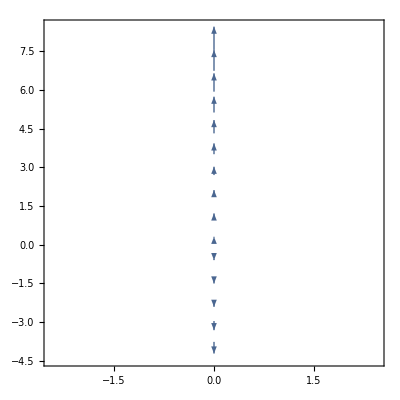

```mathematica
VectorPlot[{1,f[x,y]},{x,-2,2},{y,-4,8},Axes->True]
```

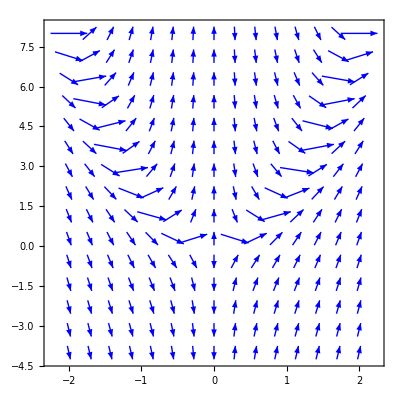

```mathematica
SlopeField = VectorPlot[{1,f[x,y]},{x,-2,2},{y,-4,8},VectorScale->{Tiny,Tiny,None},VectorStyle->Blue,Axes->True]
```

( b )  Add twenty solution curves to the slope field from part ( a ) using the StreamPoints → 20 
               option so that the general behavior of each type of solution to the DE is represented .

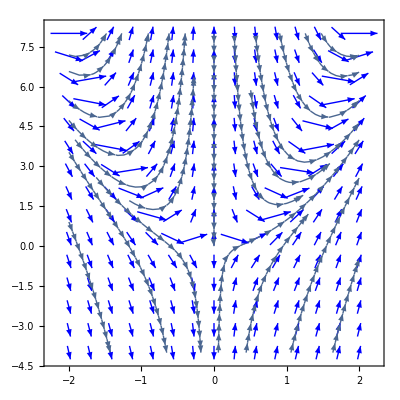

```mathematica
SlopeField = VectorPlot[{1,f[x,y]},{x,-2,2},{y,-4,8},VectorScale->{Tiny,Tiny,None},VectorStyle->Blue,Axes->True,StreamPoints->20]
```

( c )   Find the solution to the DE by hand. Then check to determine if the approximate solution
                curves plotted in part ( b ) have appropriate shapes.

( d )  Use  Mathematica  to solve the differential equation .

```mathematica
DSolve[y'[x]==4x-(2y[x])/x,y[x],x]
```

{{y[x]→x^2+C[1]/x^2}}

( e )   Use Mathematica  to find the particular solution to the DE which passes through the 
                point    P_1 =   (1/2 , 3) . Then plot the solution over the x-interval  I = [ 1/2 , 2] .

```mathematica
DSolve[{y'[x]==4x-(2y[x])/x,y[1/2]==3},y[x],x]
```

{{y[x]→(11+16 x^4)/(16 x^2)}}

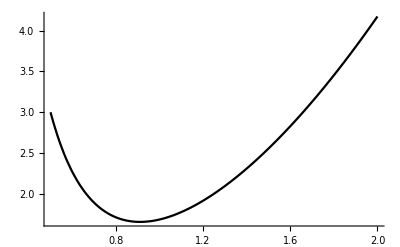

```mathematica
ExactSol=Plot[(11+16 x^4)/(16 x^2),{x,1/2,2},PlotStyle->{Black}]
```

( f )   Find and plot the Euler approximation to the solution of the DE passing through  P_1 =   (1/2 , 3) 
              using a step size of  h = 1/2  over the x - interval  I = [ 1/2 , 2 ] .

```mathematica
h=0.5;
a=0.5;
b=2;
n=Floor[(b-a)/h];
Clear[x,y];
x=ConstantArray[0,n+1];
y=ConstantArray[0,n+1];
x[[1]]=0.5;
y[[1]]=3;
Do[
x[[i+1]]=x[[i]]+h;
y[[i+1]]=y[[i]]+f[x[[i]],y[[i]]]*h;,
{i,1,n}];
x;
y;
Eulerpts1=Table[{x[[i]],y[[i]]},{i,1,n+1}]
```

{{0.5,3},{1.,-2.},{1.5,2.},{2.,3.66667}}

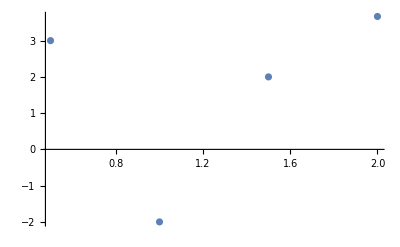

```mathematica
ListPlot[Eulerpts1]
```

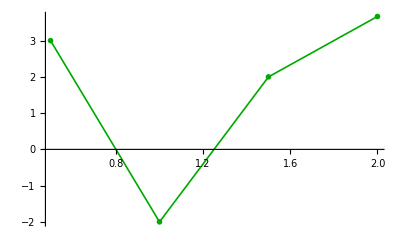

```mathematica
Euler12=ListPlot[Eulerpts1, Joined-> True,PlotMarkers->{Automatic,Tiny},PlotStyle->{Darker[Green],Thickness[0.003]}]
```

( g )   Find and plot the Euler approximation to the solution of the DE passing through  P_1 =   (1/2 , 3) 
              using a step size of  h = 1/10 over the x - interval  I = [ 1/2 , 2] .

```mathematica
h=0.1;
a=0.5;
b=2;
n=Floor[(b-a)/h];
Clear[x,y];
x=ConstantArray[0,n+1];
y=ConstantArray[0,n+1];
x[[1]]=0.5;
y[[1]]=3;
Do[
x[[i+1]]=x[[i]]+h;
y[[i+1]]=y[[i]]+f[x[[i]],y[[i]]]*h;,
{i,1,n}];
x;
y;
Eulerpts1=Table[{x[[i]],y[[i]]},{i,1,n+1}]
```

{{0.5,3},{0.6,2.},{0.7,1.57333},{0.8,1.40381},{0.9,1.37286},{1.,1.42778},{1.1,1.54222},{1.2,1.70182},{1.3,1.89818},{1.4,2.12615},{1.5,2.38242},{1.6,2.66476},{1.7,2.97167},{1.8,3.30206},{1.9,3.65516},{2.,4.03041}}

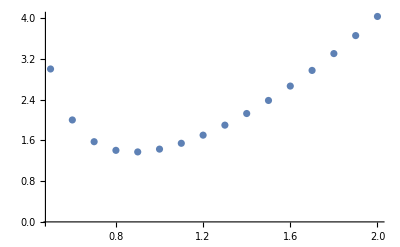

```mathematica
ListPlot[Eulerpts1]
```

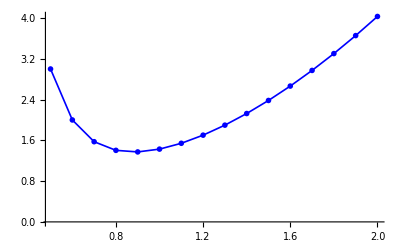

```mathematica
Euler60=ListPlot[Eulerpts1, Joined-> True,PlotMarkers->{Automatic,Tiny},PlotStyle->{Blue,Thickness[0.003]}]
```

( h )   Use the Show instruction to plot the the exact solution from (e) and the Euler approximations 
               from (f) and (g) together with a direction field for the DE over the region: 
                                    1/2  ⩽  x  ⩽  2 ,  - 2 ⩽  y  ⩽ 4 
                   on a single coordinate plane.

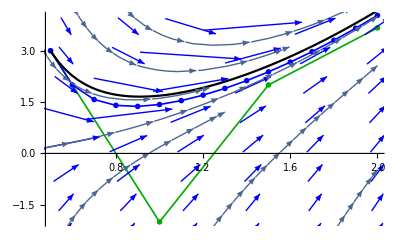

```mathematica
Show[{Euler12,Euler60,SlopeField,ExactSol},PlotRange->{{1/2,2},{-2,4}}]
```

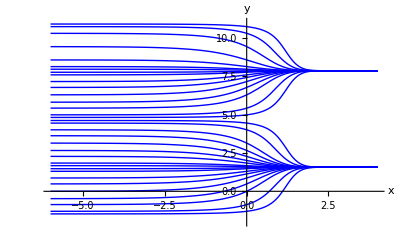
3.  A case where  Euler's Approximation  is badly behaved.
  
        Consider the differential equation      dy/dx  =  ⅇ^x cos y.
        
        This DE has the family of solutions:   
         y  =  (-1)^n  arctan ( (ⅇ^(2( ⅇ^x+C))-1)/(2 ⅇ^(ⅇ^x+C)) ) + n ℼ , where  n = 0,  ± 1,  ± 2,  ± 3, . . . .
       Some of these solution curves are displayed below:

                      -Graphics-

     ( a )  Plot a direction field for this DE over the plane region  x ∈ [ 0 , 5 ] ,  y ∈ [ -7 , 26 ] .

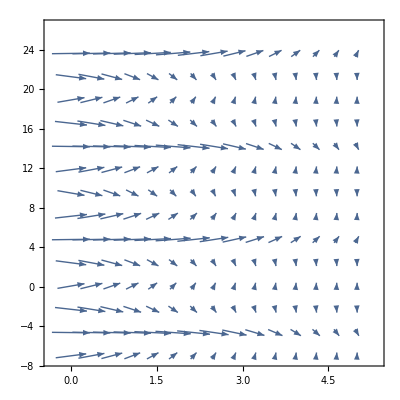

```mathematica
Clear[x,y];
f[x_,y_]:=ⅇ^x Cos[y];
Graph1 = VectorPlot[{1,f[x,y]},{x,0,5},{y,-7,26},VectorScale->{0.02,0.02,None},Axes->True]
```

( b )  Plot a graph of the Euler approximation using a step size of  h = 1/2 over the  interval
              I  =  [ 0 , 5 ]   passing through the initial point   P_1  = ( 0 , 0 ) .

```mathematica
h=0.5;
a=0;
b=5;
n=Floor[(b-a)/h];
Clear[x,y];
x=ConstantArray[0,n+1];
y=ConstantArray[0,n+1];
x[[1]]=0;
y[[1]]=0;
Do[
x[[i+1]]=x[[i]]+h;
y[[i+1]]=y[[i]]+f[x[[i]],y[[i]]]*h;,
{i,1,n}];
x;
y;
Eulerpts1=Table[{x[[i]],y[[i]]},{i,1,n+1}]
```

{{0,0},{0.5,0.5},{1.,1.22344},{1.5,1.68611},{2.,1.42828},{2.5,1.95302},{3.,-0.318914},{3.5,9.21746},{4.,-6.98572},{4.5,13.8492},{5.,26.6335}}

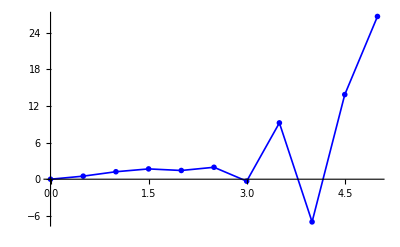

```mathematica
EulerDos=ListPlot[Eulerpts1, Joined-> True,PlotMarkers->{Automatic,Tiny},PlotStyle->{Blue,Thickness[0.003]}]
```

( c )  Use the Show instruction to merge the plots obtained from parts ( a ) and ( b ). 
            Then explain what seems to be happening to this Euler approximation for  0 ⩽ x ⩽ 3 , and then for  x > 3 .

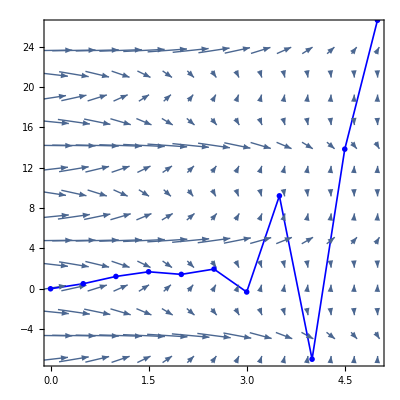

```mathematica
Show[{Graph1,EulerDos},PlotRange->{{0,5},{-7,26}}]
```